```mathematica
Integrate[ξ^2 / (ξ^2 - 1)^(1/2),{ξ,1,x}]
```

ConditionalExpression[1/2 (x √(-1+x^2)+Log[x+√(-1+x^2)]),Re[x]>1&&Im[x]==0]

```mathematica
F[x_]:=1/2 (x √(-1+x^2)+Log[x+√(-1+x^2)])
G[p_,R_]:=p^4/R^4*(F[R/p] - F[1])
```

```mathematica
G[p,R]
```

(p^4 ((R √(-1+R^2/p^2))/p+Log[R/p+√(-1+R^2/p^2)]))/(2 R^4)

```mathematica
Simplify[(p^4 ((R √(-1+R^2/p^2))/p+Log[R/p+√(-1+R^2/p^2)]))/(2 R^4)]
```

```mathematica
(p^3 (R √(-1+R^2/p^2)+p Log[R/p+√(-1+R^2/p^2)]))/(2 R^4)
FortranForm[(p^3 (R √(-1+R^2/p^2)+p Log[R/p+√(-1+R^2/p^2)]))/(2 R^4)]
```

(p^3 (R √(-1+R^2/p^2)+p Log[R/p+√(-1+R^2/p^2)]))/(2 R^4)

(p**3*(R*Sqrt(-1 + R**2/p**2) + p*Log(R/p + Sqrt(-1 + R**2/p**2))))/(2.*R**4)

```mathematica
Function[ξ,√(-1+ξ^2)]
```

Function[ξ,√(-1+ξ^2)]

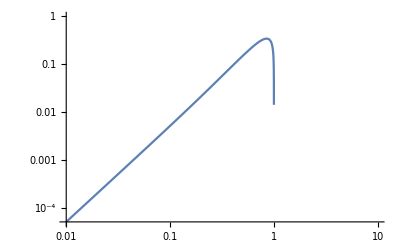

```mathematica
LogLogPlot[G[p,1],{p,0.01,10}]
```

```mathematica
Plot[ArcTanh[ξ/(√(-1+ξ^2))],{ξ,2,10}]
```

-Graphics-

```mathematica
Integrate[ξ / (ξ^2 - 1)^(1/2),ξ]
```

√(-1+ξ^2)

```mathematica
F[x_]:=(Sqrt[x^2-1])
G[p_,R_]:=(p^3/R^3)*(F[R/p] - F[1])
```

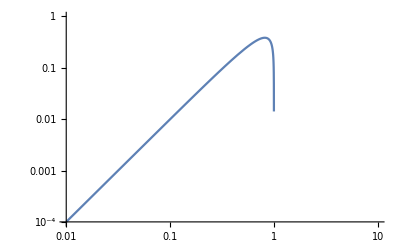

```mathematica
LogLogPlot[G[p,1],{p,0.01,10}]
```